# 3R Free Throw Gerik Zatorski

```mathematica
Quit[];
```

## Initialization

```mathematica
(* SE(2) representation of rigid body motion in the plane *)
g[x_,y_,θ_]={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
(* unhat takes a 3x3 matrix that is assumed to be ginv.gdot for SE(2) and returns a 3x1 vector. The first two components are the linear velocities in x and y and the third component is the angular velocity (around the "z" axis that is out of the plane of motion *)
unhat[a_]:={a[[1,3]],a[[2,3]],a[[2,1]]};
(* hat[] takes a 3x1 vector and creates a 3x3 matrix *)
hat[a_]:={{0,-a[[3]],a[[1]]},{a[[3]],0,a[[2]]},{0,0,0}};
(* Hom[] takes a point in the plane and adds a 1 to the end of it to create a homogeneous representation of that point. This is used for animation *)
Hom[pt_]:=Flatten[{pt,1}];
(* UnHom[] takes a homogeneous representation of a point and returns the point in the plane by removing the 1 at the end *)
UnHom[pt_]:={pt[[1]],pt[[2]]};
(* Distance between two points in 2D plane *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];

(* Helpers *)
headlist={Or,And,Equal,Unequal,Less,LessEqual,Greater,GreaterEqual,Inequality};
getAllVariables[f_?NumericQ]:=Sequence[]
getAllVariables[{}]:=Sequence[]
getAllVariables[t_]/;MemberQ[headlist,t]:=Sequence[]
getAllVariables[ll_List]:=Flatten[Union[Map[getAllVariables[#]&,ll]]]
getAllVariables[Derivative[n_Integer][f_][arg__]]:=getAllVariables[{arg}]
getAllVariables[f_Symbol[arg__]]:=Module[{fvars},If[MemberQ[Attributes[f],NumericFunction]||MemberQ[headlist,f],fvars=getAllVariables[{arg}],(*else*)fvars=f[arg]];
fvars]
getAllVariables[other_]:=other
extractVariables[formula_]:=With[{pat=_Symbol[___][___]|Subscript[_Symbol,__][___]|Subscript[_Symbol,__]|_Symbol},Union@Cases[formula,pat,-1]]
```

## Phase 1 (start -> rolling)

```mathematica
(* Conversions *)
FtToM=0.3048;

(* Robot Link Lengths Constants *)
L1=0.3048*11/12;
L2=0.3048*12/12;
L3=0.3048*8.5/12;

(* Ball Constants *)
m=0.625;
diameterBall=9.55/12*FtToM;
rball=diameterBall/2;

(* World to Joint Frame Transformations *)
g0=g[2,0,0].g[0,0,θ0[t]]; 
g1=g0.g[L1,0,0].g[0,0,θ1[t]];
g2=g1.g[L2,0,0].g[0,0,θ2[t]];
gEE=g2.g[L3,0,0].g[0,0,0];


(* World to Ball Frame Transformations prior to roll*)
gballbefore=g2.g[L3/2,-rball,0];
gline1before=gballbefore.g[-rball,0,0];
gline2before=gballbefore.g[rball,0,0];
g2ballbefore=Inverse[g2].gballbefore;


(* Fake Joint Velocities *)
tMax = 5/8;
θ0sol=ListInterpolation[{0,5*Pi/12},{0,tMax}][t];
θ1sol=ListInterpolation[{Pi*8/12,Pi*1/12},{0,tMax}][t];
θ2sol=ListInterpolation[{Pi*6/12,-Pi*1/12},{0,tMax}][t];

θ0dotsol=D[θ0sol,t];
θ1dotsol=D[θ1sol,t];
θ2dotsol=D[θ2sol,t];

θ0dotdotsol=D[θ0dotsol,t];
θ1dotdotsol=D[θ1dotsol,t];
θ2dotdotsol=D[θ2dotsol,t];

(*********************************** Graphic Primatives ****************************************)

coordJoint0[t_]:={g0[[1,3]],g0[[2,3]]};
coordJoint1[time_]:=({g1[[1,3]],g1[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol})/.t->time;
coordJoint2[time_]:=({g2[[1,3]],g2[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol})/.t->time;
coordEE[time_]:=({gEE[[1,3]],gEE[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol})/.t->time;
coordballbefore[time_]:=({gballbefore[[1,3]],gballbefore[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol})/.t->time;
coordline1before[time_]:=({gline1before[[1,3]],gline1before[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol})/.t->time;
coordline2before[time_]:=({gline2before[[1,3]],gline2before[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol})/.t->time;
coordg2ballbefore[time_]:=({g2ballbefore[[1,3]],g2ballbefore[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol})/.t->time;

(* Joint Graphics *)
GraphicsL1=Line[{coordJoint0[t],coordJoint1[t]}];
GraphicsL2=Line[{coordJoint1[t],coordJoint2[t]}];
GraphicsL3=Line[{coordJoint2[t],coordEE[t]}];

(* Ball Graphics *)
Graphicsballbefore = Circle[coordballbefore[t],rball];
Graphicsballlinebefore=Line[{coordline1before[t],coordline2before[t]}];

 (* Other Graphics *)
GraphicsDebug = Text[t,{2,0.1}];

(*********************************** Solving ****************************************)

(* Solving for conditions at roll *)
troll=0.05;
tr=gballbefore/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol}/.t->troll;
xr=tr[[1,3]];
yr=tr[[2,3]];
θr=(θ0[t]+θ1[t]+θ2[t])/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol}/.t->troll;

(* dot sol estimation *)
(*tr1=gballbefore/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol}/.t->(troll-.01);
tr2=gballbefore/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol}/.t->(troll+.01);
xrdot=N[(tr2[[1,3]]-tr1[[1,3]])/.02];
yrdot=N[(tr2[[2,3]]-tr1[[2,3]])/.02];
θrdot=N[(ArcCos[tr2[[1,1]]]-ArcCos[tr1[[1,1]]])/.02];*)

(* dot sol exact *)
θrdot=θ2dotsol/.t->troll;
trdot=D[gballbefore,t]/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol,θ0'[t]->θ0dotsol,θ1'[t]->θ1dotsol,θ2'[t]->θ2dotsol};
xrdot=trdot[[1,3]]/.t->troll;
yrdot=trdot[[2,3]]/.t->troll;

(*********************************** Animations ****************************************)

graphics = Graphics[{
Black,GraphicsL1/.t->time,
Black,GraphicsL2/.t->time,
Black,GraphicsL3/.t->time,
Black,Graphicsballbefore/.t->time,
Black,Graphicsballlinebefore/.t->time,
Black, GraphicsDebug/.t->time
},
PlotRange->{{-1,8},{-1,8}},
Axes->True];

frames=Table[graphics,{time,0,5/8,0.1}];
anim=ListAnimate[frames,AnimationRate->0.2];
Export["~/Desktop/Shot_Kinematics_Calculate_Conditions_At_Release.gif",frames];

Animate[
Show[
Graphics[{
Black,GraphicsL1/.t->time,
Black,GraphicsL2/.t->time,
Black,GraphicsL3/.t->time,
Black,Graphicsballbefore/.t->time,
Black,Graphicsballlinebefore/.t->time,
Black, GraphicsDebug/.t->time
},
(*PlotRange->{{-1,8},{-1,8}},*)
Axes->True]
],
{time,0,5/8},
AnimationRunning->False,
AnimationRate->1.0
]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1}.

## Phase 2 (rolling -> release)

```mathematica
(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* New Ball Frame Transforms for time after roll *)
gball=g[x[t],y[t],0].g[0,0,θ[t]];
gline1=gball.g[-rball,0,0];
gline2=gball.g[rball,0,0];
g2ball=Inverse[g2].gball; (* what the ball looks like relative to the wrist frame *)
θ2ball=θ[t]-(θ0[t]+θ1[t]+θ2[t]);
gcontact=g2.g[L3/2+rball*θ2ball,0,0];

(* Gotta do this *)
θ0[t]=θ0sol;
θ1[t]=θ1sol;
θ2[t]=θ2sol;

(* Lagrangian using body velocities (see lecture 23) *)
Vball=unhat[Inverse[gball].D[gball,t]];
Iball=DiagonalMatrix[{m,m,J}];
J=m*rball^2;
KE=1/2*(Vball.Iball).{Vball}ᵀ;
PE=m*grav*y[t];
Lag =KE-PE;

(***************************************************************************)
(* Constraints and External forces *)
(***************************************************************************)

(* External forces *)
Fhandx=m*D[D[Inverse[gcontact][[1,3]],t],t];
Fhandy=m*D[D[Inverse[gcontact][[2,3]],t],t];

(* Constraints *)
(* Ball rolls without slipping where x=rball*θ *)
ϕa=g2ball[[1,3]]-rball*θ2ball;

(* Euler-Lagrange equations VECTORS *)
Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==λa*D[ϕa,x[t]]+Fhandx;
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==λa*D[ϕa,y[t]]-Fhandy;
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==λa*D[ϕa,θ[t]];
Eq4=D[D[ϕa,t],t]==0;
(*Eq5=D[D[ϕb,t],t]==0;*)

ELtemp=Solve[{Eq1&&Eq2&&Eq3&&Eq4},{x''[t],y''[t],θ''[t],λa}];
EL={x''[t]==ELtemp[[1,1,2]],y''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Unconstrainted test *)
(*Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==0;
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==0;
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==0;
ELtemp=Solve[{Eq1&&Eq2&&Eq3},{x''[t],y''[t],θ''[t]}];
EL={x''[t]==ELtemp[[1,1,2]],y''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};*)

(* Constants *)
grav = 9.8;

(* Initial Condition *)
InitCon={x[troll]==xr,y[troll]==yr,θ[troll]==θr,x'[troll]==xrdot,y'[troll]==yrdot,θ'[troll]==θrdot};

(* Numerical Solution *)
tmax =5/8;
(*sol=NDSolve[Join[EL,InitCon],{x,y,θ},{t,troll,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},WorkingPrecision->30,AccuracyGoal->8,PrecisionGoal->8,MaxSteps->20000
];*)
sol=NDSolve[Join[EL,InitCon],{x,y,θ},{t,troll,tmax}];

xsol=x[t]/.sol;
ysol=y[t]/.sol;
θsol=θ[t]/.sol;

coordball[time_]:=({gball[[1,3]],gball[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordline1[time_]:=({gline1[[1,3]],gline1[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordline2[time_]:=({gline2[[1,3]],gline2[[2,3]]}/.{θ0[t]->θ0sol,θ1[t]->θ1sol,θ2[t]->θ2sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;

Graphicsball = Circle[{coordball[t][[1]][[1]],coordball[t][[2]][[1]]},rball];
Graphicsballline=Line[{{coordline1[t][[1]][[1]],coordline1[t][[2]][[1]]},{coordline2[t][[1]][[1]],coordline2[t][[2]][[1]]}}];


Animate[
Show[
Graphics[{
Black,GraphicsL1/.t->time,
Black,GraphicsL2/.t->time,
Black,GraphicsL3/.t->time,
Black,Graphicsball/.t->time,
Black,Graphicsballline/.t->time,
Black, GraphicsDebug/.t->time
}],
(*PlotRange->{{-1,8},{-1,8}},*)
Axes->True
],
{time,troll,tmax},
AnimationRunning->False,
AnimationRate->1.0
]

graphics = Graphics[{
Black,GraphicsL1/.t->time,
Black,GraphicsL2/.t->time,
Black,GraphicsL3/.t->time,
Black,Graphicsball/.t->time,
Black,Graphicsballline/.t->time,
Black, GraphicsDebug/.t->time
},PlotRange->{{-1,8},{-1,8}},Axes->True]

frames=Table[graphics,{time,troll,tmax,0.1}];
anim=ListAnimate[frames,AnimationRate->0.2];
Export["~/Desktop/Dropping_The_Ball_Figuratively_Speaking.gif",frames];
```

-Graphics-

## Phase 3 (Simulate after Release)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Backboard!

0.890143

Front Rim Impact!

0.987409

-1.11818

-3.90736

Ground Impact

1.44888

Ground Impact

2.82517

Ground Impact

3.9262

Ground Impact

4.80702

Set::shape: Lists {times} and {} are not the same shape.

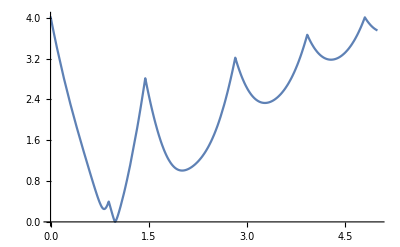

```mathematica
(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian *)
Iball=2/3*m*rball^2;
KE=1/2*m*(x'[t]^2+y'[t]^2)+1/2*Iball*θ'[t]^2;
PE=m*g*y[t];
L=KE-PE;

(* Euler-Lagrange equations *)
Eq=(Thread[D[L,qᵀ]-D[D[L,dqᵀ],t]==0]);
ELtemp=Solve[Eq[[1]]&&Eq[[2]]&&Eq[[3]],{y''[t],x''[t],θ''[t]}];
EL={y''[t]==ELtemp[[1,1,2]],x''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Hamiltonian *)
p=D[L,dqᵀ];
H=p.dq-L;

(* Impact Equations - solving for velocities after impact *)
(* Impact with ground *)
ϕ0=y[t]-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ0dq1p)/.(y'[t]->ϕ0dq2p)/.(θ'[t]->ϕ0dq3p))-(D[L,dqᵀ])==λ*D[ϕ0,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ0dq1p)/.(y'[t]->ϕ0dq2p)/.(θ'[t]->ϕ0dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ0dq1p,ϕ0dq2p,ϕ0dq3p,λ}];
ϕ0dq1p=IEq[[1,1,2]]*c;
ϕ0dq2p=IEq[[1,2,2]]*c;
ϕ0dq3p=IEq[[1,3,2]];
(* Impact with backboard *)
ϕ1=x[t]+rball+BaselineToBackboard;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ1dq1p)/.(y'[t]->ϕ1dq2p)/.(θ'[t]->ϕ1dq3p))-(D[L,dqᵀ])==λ*D[ϕ1,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ1dq1p)/.(y'[t]->ϕ1dq2p)/.(θ'[t]->ϕ1dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ1dq1p,ϕ1dq2p,ϕ1dq3p,λ}];
ϕ1dq1p=IEq[[1,1,2]]*c;
ϕ1dq2p=IEq[[1,2,2]]*c;
ϕ1dq3p=IEq[[1,3,2]];
(* Impact with front rim *)
ϕ2=Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2}]-RimThickness/2-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ2dq1p)/.(y'[t]->ϕ2dq2p)/.(θ'[t]->ϕ2dq3p))-(D[L,dqᵀ])==λ*D[ϕ2,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ2dq1p)/.(y'[t]->ϕ2dq2p)/.(θ'[t]->ϕ2dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ2dq1p,ϕ2dq2p,ϕ2dq3p,λ}];
ϕ2dq1p=IEq[[2,1,2]]*c;
ϕ2dq2p=IEq[[2,2,2]]*c;
ϕ2dq3p=IEq[[2,3,2]];
(* Impact with back rim *)
ϕ3=Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2}]-RimThickness/2-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ3dq1p)/.(y'[t]->ϕ3dq2p)/.(θ'[t]->ϕ3dq3p))-(D[L,dqᵀ])==λ*D[ϕ3,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ3dq1p)/.(y'[t]->ϕ3dq2p)/.(θ'[t]->ϕ3dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ3dq1p,ϕ3dq2p,ϕ3dq3p,λ}];
ϕ3dq1p=IEq[[1,1,2]]*c;
ϕ3dq2p=IEq[[1,2,2]]*c;
ϕ3dq3p=IEq[[1,3,2]];

(* Constants *)
g=9.8;
(* Coefficient of Restitution *)
c=0.8;

(* Initial Conditions - TODO: replace these with results from shot dynamics.08.08*)
(* Impacts with backboard, front rim *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==6.5*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* Impacts with backboard, back rim *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==5.5*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* Impacts with backboard, MAYBE front rim back rim *)
InitCon={x[0]==-BaselineToFoulLine,y[0]==5.8*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};
(* Impacts with front rim - short shot *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==4.2*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* over the backboard *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==8.3*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)

(* Numerical Solution *)
tmax=5;
newxdot=0;
newydot=0;
newθdot=0;
(* TODO: better options to avoid missing (ex. "back rim" printed when tmax=5, but no change in direction) *)
{sol,{times}}=NDSolve[Join[EL,InitCon,
(* impact with ground *)
{WhenEvent[y[t]-rball==0,{Print["Ground Impact"],end=t,Print[end],newxdot=N[ϕ0dq1p],newydot=N[ϕ0dq2p],newθdot=N[ϕ0dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot},"DetectionMethod"->"Interpolation"]},
(* impact with backboard - TODO: improve y triggers*)
{WhenEvent[x[t]+rball+BaselineToBackboard==0&&y[t]<(BackboardBaseHeight+GroundToBackboard)&&y[t]>BackboardBaseHeight,{Print["Backboard!"],end=t,Print[end],newxdot=N[ϕ1dq1p],newydot=N[ϕ1dq2p],newθdot=N[ϕ1dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot},"DetectionMethod"->"Interpolation"]},
(* impact with front rim *)
{WhenEvent[Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2}]-RimThickness/2-rball==0,{Print["Front Rim Impact!"],end=t,Print[end],newxdot=N[ϕ2dq1p],newydot=N[ϕ2dq2p],newθdot=N[ϕ2dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot,Print[newxdot],Print[newydot]},
"DetectionMethod"->"Interpolation",
"IntegrateEvent"->True,
"LocationMethod"->{"Brent",AccuracyGoal->12,PrecisionGoal->12}]},
(* impact with back rim *)
{WhenEvent[Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2}]-RimThickness/2-rball==0,
{Print["Back Rim Impact!"],end=t,Print[end],newxdot=N[ϕ3dq1p],newydot=N[ϕ3dq2p],newθdot=N[ϕ3dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot,Print[newxdot],Print[newydot]},
"DetectionMethod"->"Interpolation",
"LocationMethod"->{"Brent",AccuracyGoal->12,PrecisionGoal->12}]}
],{x,y,θ},{t,0,tmax}]//Reap;



(*ListPlot[RealExponent[Differences[times]]]*)

xsol=First[x[t]/.sol];
ysol=First[y[t]/.sol];
θsol=First[θ[t]/.sol];

Plot[Distance2D[{xsol,ysol},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2,0}]-RimThickness/2-rball,{t,0,tmax}]

(* Dynamic Graphics *)
BallGraphic=Circle[{xsol,ysol},diameterBall/2];
BallLineGraphic=Line[{{xsol-rball*Cos[θsol],ysol-rball*Sin[θsol]},{xsol+rball*Cos[θsol],ysol+rball*Sin[θsol]}}];

(* Static Graphics *)
FloorGraphic=Line[{{-22*FtToM,0},{0,0}}];
BackboardGraphic=Line[{{-BaselineToBackboard,BackboardBaseHeight},{-BaselineToBackboard,BackboardBaseHeight+GroundToBackboard}}];
FrontRimGraphic=Disk[{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2},RimThickness/2];
BackRimGraphic=Disk[{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2},RimThickness/2];
NetFrontGraphic=Line[{{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2-.2}}];
NetBackGraphic=Line[{{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2},{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2-.2}}];
HitchGraphic=Line[{{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2},{-BaselineToBackboard,GroundToRim-RimThickness/2}}];

(*Animate[
Show[
Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
}],
PlotRange->{{-8,1},{-1,6}},
Axes->True,
ImageSize->Full
],
{time,0,tmax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{1000,800}
]

Animate[
Show[
Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
}],
PlotRange->{{-2.5,-1},{2.5,4.1}},
Axes->True,
ImageSize->Full
],
{time,0,tmax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{800,700}
]

graphics = Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
},PlotRange->{{-8,1},{-1,6}},
Axes->True]

frames=Table[graphics,{time,0,tmax,0.1}];
anim=ListAnimate[frames,AnimationRate->0.4];
Export["~/Desktop/Court_View.gif",frames];

graphics = Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
},
PlotRange->{{-2.5,-1},{2.5,4.1}},Axes->True]

frames=Table[graphics,{time,0,tmax,0.01}];
anim=ListAnimate[frames,AnimationRate->0.4];
Export["~/Desktop/Basket_View.gif",frames];*)
```